## Gravito-scalar QNMs of Schwarzschild BHs for BD Reference: Paolo Pani, “Advanced methods in Black-Hole Perturbation Theory” (2013) O. Tattersall, “General theories of linear gravitational perturbations to a Schwarzschild Black Hole”

#### Perturbation equations:

```mathematica
Clear[u1,u2];
ϵa=1;
F[r_]:=1-2M/r;
VRW[s_]:=F[r]((l(l+1))/r^2+(2(1-s^2)M)/r^3);
S1 = 4(2b-1)(9 M^2+(l^2+l -4) M r +r^2(2-l-l^2+r^2 ω^2))/(r^3(6 M + ( l + 2 ) (l - 1) r ));
(* note that this S1 in contrast to DCS goes as r^-1 far from the system, not r^-5. As we expand in a series of r^-1 this meens that the terms will couple stronger and we will need to find higher order terms than DCS *)
S2 = 0;
e1=F[r]^2 u1''[r]+F'[r]F[r]u1'[r]+(ω^2-VRW[2])u1[r] + S1 u2[r]
e2=F[r]^2 u2''[r]+F'[r]F[r]u2'[r]+(ω^2-VRW[0])u2[r]  (* expressed in radial coords. If in tortoise coords F[r]^2 u1''[r]+F'[r]F[r]u1'[r] = u1''[r*] *)
```

(-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u1[r]+(4 (-1+2 b) (9 M^2+(-4+l+l^2) M r+r^2 (2-l-l^2+r^2 ω^2)) u2[r])/(r^3 (6 M+(-1+l) (2+l) r))+(2 M (1-(2 M)/r) u1'[r])/r^2+(1-(2 M)/r)^2 u1''[r]

(-((2 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u2[r]+(2 M (1-(2 M)/r) u2'[r])/r^2+(1-(2 M)/r)^2 u2''[r]

#### Series at the horizon [arbitrary order]

```mathematica
Clear[u1,u2];

u1[r_]:=(r-2M)^bb G1[r]; 
u2[r_]:=(r-2M)^bb G2[r];(* Frobenius solution eq. 30 back in radial coordinates*)
Es1=FullSimplify[(r^6 e1)/(-2 M+r)^bb]
Es2=FullSimplify[e2/(1/(r^9 β ω Gamma[-1+l])(-2 M+r)^bb)];
```

r^3 (((-12 M^2+2 (3+bb+l+l^2) M r+r^2 ((-1+bb) bb-l (1+l)+r^2 ω^2)) G1[r])/r+(4 (-1+2 b) (9 M^2+(-4+l+l^2) M r-(-2+l+l^2) r^2+r^4 ω^2) G2[r])/(6 M+(-2+l+l^2) r)-(2 M-r) (2 (M+bb r) G1'[r]+r (-2 M+r) G1''[r]))

```mathematica
ORD=5;
G1[r_]:=Sum[u1h[i](r-2M)^i,{i,0,ORD+3}];
G2[r_]:=Sum[u2h[i](r-2M)^i,{i,0,ORD+3}];
ss=Series[{Es1,Es2}/.{bb->-2 ⅈ M ω},{r,2M,ORD+3}];
(*FullSimplify[Series[Es1/.{bb->-2 ⅈ M ω},{r,2M,1}]] *)(* series expansion of the equation of motion in r around 2M as the Frobenius expansion is around r - r+ = r - 2M *)
yh=Union[Table[u1h[i],{i,1,ORD}],Table[u2h[i],{i,1,ORD}]];
EQsh=Union[Table[Normal[Series[SeriesCoefficient[ss[[1]],i],{J,0,1}]]==0,{i,1,ORD}],Table[Normal[Series[SeriesCoefficient[ss[[2]],i],{J,0,1}]]==0,{i,1,ORD}]];
Length[yh]
Length[EQsh]
seriesH=Solve[EQsh,yh][[1]];

Clear[u1,u2,G1,G2]
```

10

10

```mathematica
Solve[bb^2 M^2+4 M^4 ω^2==0,bb] (* why does bb comes from this? *)
```

{{bb→-2 ⅈ M ω},{bb→2 ⅈ M ω}}

```mathematica
seriesH//.{kk^2->-ω^2,n->-(2 M ω^2)/kk, M->1, u1h[0]->1,u2h[0]->1, l -> 10 }
```

{u1h[1]→-(-1401231+5439156 b-4771800 ⅈ ω-1052460 ⅈ b ω+198072 ω^2-790416 b ω^2+347904 ⅈ ω^3+92736 ⅈ b ω^3-14208 ω^4+28416 b ω^4)/(24642 (ⅈ+4 ω)^2),u1h[2]→-1/(87528384 (ⅈ+2 ω)^2 (ⅈ+4 ω)^2)(100963131408-327223144512 b-47217612492 ⅈ ω+846347807736 ⅈ b ω+412575399720 ω^2+196830612144 b ω^2+31783926672 ⅈ ω^3-178054979616 ⅈ b ω^3-63204212736 ω^4-27991643904 b ω^4-2186118144 ⅈ ω^5+12774961152 ⅈ b ω^5+2243045376 ω^6+1115725824 b ω^6+151400448 ⅈ ω^7-302800896 ⅈ b ω^7),u1h[3]→-((-12418919721332784+37994758944210432 b+29686096771800804 ⅈ ω-155146556183656680 ⅈ b ω-20218635725304960 ω^2-167900272989483456 b ω^2+45400312030443552 ⅈ ω^3+60474504498750144 ⅈ b ω^3-2707659126774432 ω^4+47014430904304704 b ω^4-12239771189856768 ⅈ ω^5-10495633988611584 ⅈ b ω^5+383262766566912 ω^6-5125976830725120 b ω^6+914195198361600 ⅈ ω^7+783176491008000 ⅈ b ω^7-32532609097728 ω^8+244144090497024 b ω^8-19854049148928 ⅈ ω^9-19984859136000 ⅈ b ω^9+1971839434752 ω^10-3943678869504 b ω^10)/(174881711232 (ⅈ+2 ω)^2 (ⅈ+4 ω)^2 (3 ⅈ+4 ω)^2)),u1h[4]→-((611797663746871771968-1815049225807987697280 b-2237872374457687539936 ⅈ ω+9316102284885964980672 ⅈ b ω-1213029956889828849744 ω^2+15681756501493354703520 b ω^2-2009051699115224106144 ⅈ ω^3-11285844101072845624512 ⅈ b ω^3-1190232238866097280256 ω^4-6032263366913155250688 b ω^4+243234107327149312896 ⅈ ω^5+3762220701837942782208 ⅈ b ω^5+635426291562736776192 ω^6+1168816116406252603392 b ω^6-5144091124202721792 ⅈ ω^7-551072037619747593216 ⅈ b ω^7-80407962287891030016 ω^8-120998459743023071232 b ω^8-269035194826874880 ⅈ ω^9+40293580040601845760 ⅈ b ω^9+3766392231775174656 ω^10+6063599837073899520 b ω^10+160743338154786816 ⅈ ω^11-1381633600334856192 ⅈ b ω^11-49776397658357760 ω^12-112476589488340992 b ω^12-7959060991180800 ⅈ ω^13+15918121982361600 ⅈ b ω^13)/(2484719353184256 (ⅈ+ω)^2 (ⅈ+2 ω)^2 (ⅈ+4 ω)^2 (3 ⅈ+4 ω)^2)),u1h[5]→-((-172910070983609149460961600+502456128646866575857603200 b+790273208870659778622219360 ⅈ ω-2965457337469552505965590720 ⅈ b ω+970683386827858463276133264 ω^2-6293504245565487325320253728 b ω^2-26568161858071040251933440 ⅈ ω^3+6418948688091931128869099520 ⅈ b ω^3+367097715100423778721719616 ω^4+4263179582608451584402474368 b ω^4-78669001043092894823648640 ⅈ ω^5-2788773479000922285010033920 ⅈ b ω^5-177868680646166550511347456 ω^6-1502830409861934925815218688 b ω^6+127204716854360421256757760 ⅈ ω^7+614148406970997162246773760 ⅈ b ω^7+19957114120327722054890496 ω^8+273334288001351406133598208 b ω^8-27274160839935725669007360 ⅈ ω^9-79195174497298006250618880 ⅈ b ω^9-1465394193986241744470016 ω^10-27149813477106694952583168 b ω^10+2161539781691729565450240 ⅈ ω^11+5771532504864320355041280 ⅈ b ω^11+25100346835121553801216 ω^12+1455467674442044321824768 b ω^12-65971365388071657799680 ⅈ ω^13-212848853324599331389440 ⅈ b ω^13+4472690848043995496448 ω^14-37187695752121518391296 b ω^14+394030824302586101760 ⅈ ω^15+2977580225532631449600 ⅈ b ω^15-154922803830894624768 ω^16+309845607661789249536 b ω^16)/(13790192410172620800 (ⅈ+ω)^2 (ⅈ+2 ω)^2 (ⅈ+4 ω)^2 (3 ⅈ+4 ω)^2 (5 ⅈ+4 ω)^2)),u2h[1]→-(ⅈ (-111+2 ⅈ ω+8 ω^2))/(2 (ⅈ+4 ω)),u2h[2]→-(12320+4 ⅈ ω-1784 ω^2+48 ⅈ ω^3+64 ω^4)/(16 (ⅈ+2 ω) (ⅈ+4 ω)),u2h[3]→-(1342440 ⅈ-75228 ω-298368 ⅈ ω^2-5280 ω^3+21664 ⅈ ω^4+768 ω^5-512 ⅈ ω^6)/(96 (ⅈ+2 ω) (ⅈ+4 ω) (3 ⅈ+4 ω)),u2h[4]→-(-140849280-21458016 ⅈ ω+44161584 ω^2+1224960 ⅈ ω^3-4845312 ω^4+172160 ⅈ ω^5+236288 ω^6-10240 ⅈ ω^7-4096 ω^8)/(3072 (ⅈ+ω) (ⅈ+2 ω) (ⅈ+4 ω) (3 ⅈ+4 ω)),u2h[5]→-((-13924310400 ⅈ+4112643360 ω+6062719056 ⅈ ω^2-655771680 ω^3-903367040 ⅈ ω^4+208000 ω^5+66381312 ⅈ ω^6+3504640 ω^7-2447360 ⅈ ω^8-122880 ω^9+32768 ⅈ ω^10)/(30720 (ⅈ+ω) (ⅈ+2 ω) (ⅈ+4 ω) (3 ⅈ+4 ω) (5 ⅈ+4 ω)))}

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["seriesH_BD.mx",{seriesH,ORD}];*)
```

#### Series at infinity [arbitrary order]

```mathematica
u1[r_]:=Exp[kk r] r^n G1[r];
u2[r_]:=Exp[kk r] r^n G2[r]; 
(* the frobeniussolution, eq (30) evaluated at r >> r+, see also eq. (11) *)
Es1=FullSimplify[e1/(ⅇ^(kk r) r^n)]
Es2=FullSimplify[e2/(ⅇ^(kk r) r^n)]
```

(-((2 M-r) (6 M-l (1+l) r))/r^4+ω^2) G1[r]+(4 (-1+2 b) (9 M^2+(-4+l+l^2) M r-(-2+l+l^2) r^2+r^4 ω^2) G2[r])/(r^3 (6 M+(-2+l+l^2) r))+(2 M (-2 M+r) ((n+kk r) G1[r]+r G1'[r]))/r^4+((-2 M+r)^2 (((-1+n) n+2 kk n r+kk^2 r^2) G1[r]+r (2 (n+kk r) G1'[r]+r G1''[r])))/r^4

1/r^4(((2 M-r) (r (l+l^2+n-n^2-2 kk n r-kk^2 r^2)+2 M ((-1+n)^2+kk (-1+2 n) r+kk^2 r^2))+r^4 ω^2) G2[r]+r (-2 M+r) (2 (M-2 M n-2 kk M r+n r+kk r^2) G2'[r]+r (-2 M+r) G2''[r]))

```mathematica
(* The inclusion of the mixing term causes a dependence of u1inf[3] on u2inf[4], so we need to change the orders such that we can solve this lower order of u1 in terms of one higher in u2 *)

ORDinf=2;

G1[r_]:=Sum[u1inf[i]/r^i,{i,0,ORDinf+3}];
G2[r_]:=Sum[u2inf[i]/r^i,{i,0,ORDinf+3}];

ruleINF={kk^2->-ω^2,n->-(2 M ω^2)/kk};
ss=Series[{Es1,Es2},{r,∞,ORDinf+3}]/.ruleINF; 

yinf=Union[Table[u1inf[i],{i,1,ORDinf+1}],Table[u2inf[i],{i,1,ORDinf+2}]];

EQsinf=Union[Table[SeriesCoefficient[ss[[1]],i]==0,{i,2,ORDinf+2}],Table[SeriesCoefficient[ss[[2]],i]==0,{i,2,ORDinf+3}]];

Length[yinf]
Length[EQsinf]
seriesINF=Solve[EQsinf,yinf][[1]]//Simplify;
Print["Should all be zero if all higher terms are expressed in terms of the BC"]
seriesINF /. {u1inf[0] ->0,u2inf[0] ->0} 
Clear[u1,u2,G1,G2]
```

7

7

Should all be zero if all higher terms are expressed in terms of the BC

{u1inf[1]→0,u1inf[2]→0,u1inf[3]→0,u2inf[1]→0,u2inf[2]→0,u2inf[3]→0,u2inf[4]→0}

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["seriesINF_BD.mx",{seriesINF,ORDinf}];*)
```

#### Higher order BCs at infinity

```mathematica
(*<<"seriesINF_BD.mx";*)
ORDinf2=(ORDinf+1);

y1=(Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+ (Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y1p=D[y1,r];
y2= (Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+(Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y2p=D[y2,r];
solBC=Solve[{y1==Y1,y1p==Y1p,y2==Y2,y2p==Y2p},{B1,C1,B2,C2}];
(* A list of rules for how to replace B1, B2, C1, C2 in favour of Y1 and Y1p *)
solBC=solBC[[1]];
```

```mathematica
Print["Tests:"]
solBC//.{kk^2->-ω^2,n->-(2 M ω^2)/kk, M->1, u1h[0]->1,u2h[0]->0, l -> 10,k->I ω ,ω->1,r-> 1}
Length[solBC]
Print["End of tests"]
```

Tests:

{B1→-(6 ⅈ ((124883/2+57520 ⅈ) ⅇ^ⅈ Y1+(1048+(121135 ⅈ)/6) ⅇ^ⅈ Y1p))/14404330685+(4360428/212006189690348676005+(247968 ⅈ)/212006189690348676005) ((-124883/2-57520 ⅈ) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561+(31250 ⅈ)/19683) ⅇ^ⅈ-(120011510807/34012224+(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^ⅈ-(62500/6561+(62500 ⅈ)/19683) b ⅇ^ⅈ+(1638538103977/34012224+(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ) ⅇ^-ⅈ Y2+1/14409216317 6 ⅈ (1/14404330685 6 ⅈ ((-124883/2-57520 ⅈ) ((31250 ⅈ ⅇ^-ⅈ)/19683+(35000407/314928-(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^-ⅈ-(62500 ⅈ b ⅇ^-ⅈ)/19683-(134644495/104976-(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^-ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561-(31250 ⅈ)/19683) ⅇ^-ⅈ-(120011510807/34012224-(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^-ⅈ-(62500/6561-(62500 ⅈ)/19683) b ⅇ^-ⅈ+(1638538103977/34012224-(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^-ⅈ) ⅇ^ⅈ)-(10011542688/212006189690348676005-(17548003902 ⅈ)/42401237938069735201) ((-124883/2-57520 ⅈ) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561+(31250 ⅈ)/19683) ⅇ^ⅈ-(120011510807/34012224+(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^ⅈ-(62500/6561+(62500 ⅈ)/19683) b ⅇ^ⅈ+(1638538103977/34012224+(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ) ⅇ^(-2 ⅈ)) ((125471/2+57216 ⅈ) ⅇ^ⅈ Y2+(1148+(121123 ⅈ)/6) ⅇ^ⅈ Y2p),C1→(-37728/14713227169+(726810 ⅈ)/14713227169) ⅇ^-ⅈ Y1+(1828072512/42386837917160476153-(87804895686 ⅈ)/211934189585802380765) ⅇ^(-2 ⅈ) ((124883/2+57520 ⅈ) ⅇ^ⅈ Y1+(1048+(121135 ⅈ)/6) ⅇ^ⅈ Y1p)+(41328/14718225673-(726738 ⅈ)/14718225673) ((-37728/14713227169+(726810 ⅈ)/14713227169) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^-ⅈ-(1828072512/42386837917160476153-(87804895686 ⅈ)/211934189585802380765) ((-124883/2-57520 ⅈ) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561+(31250 ⅈ)/19683) ⅇ^ⅈ-(120011510807/34012224+(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^ⅈ-(62500/6561+(62500 ⅈ)/19683) b ⅇ^ⅈ+(1638538103977/34012224+(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ) ⅇ^(-2 ⅈ)) ⅇ^-ⅈ Y2+1/14409216317 6 ⅈ ((-37728/14713227169+(726810 ⅈ)/14713227169) ((31250 ⅈ ⅇ^-ⅈ)/19683+(35000407/314928-(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^-ⅈ-(62500 ⅈ b ⅇ^-ⅈ)/19683-(134644495/104976-(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^-ⅈ) ⅇ^-ⅈ-(1828072512/42386837917160476153-(87804895686 ⅈ)/211934189585802380765) ((-124883/2-57520 ⅈ) ((31250 ⅈ ⅇ^-ⅈ)/19683+(35000407/314928-(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^-ⅈ-(62500 ⅈ b ⅇ^-ⅈ)/19683-(134644495/104976-(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^-ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561-(31250 ⅈ)/19683) ⅇ^-ⅈ-(120011510807/34012224-(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^-ⅈ-(62500/6561-(62500 ⅈ)/19683) b ⅇ^-ⅈ+(1638538103977/34012224-(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^-ⅈ) ⅇ^ⅈ) ⅇ^(-2 ⅈ)+(14623336585/14718225673+(1668590448 ⅈ)/14718225673) ((-37728/14713227169+(726810 ⅈ)/14713227169) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^-ⅈ-(1828072512/42386837917160476153-(87804895686 ⅈ)/211934189585802380765) ((-124883/2-57520 ⅈ) (-(31250 ⅈ ⅇ^ⅈ)/19683+(35000407/314928+(112451422895 ⅈ)/102036672) (1-2 b) ⅇ^ⅈ+(62500 ⅈ b ⅇ^ⅈ)/19683-(134644495/104976+(1533748283665 ⅈ)/102036672) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ-(1048+(121135 ⅈ)/6) ((31250/6561+(31250 ⅈ)/19683) ⅇ^ⅈ-(120011510807/34012224+(101143684331 ⅈ)/34012224) (1-2 b) ⅇ^ⅈ-(62500/6561+(62500 ⅈ)/19683) b ⅇ^ⅈ+(1638538103977/34012224+(1405146606235 ⅈ)/34012224) (-1+2 b) ⅇ^ⅈ) ⅇ^ⅈ) ⅇ^(-2 ⅈ)) ⅇ^(-2 ⅈ)) ((125471/2+57216 ⅈ) ⅇ^ⅈ Y2+(1148+(121123 ⅈ)/6) ⅇ^ⅈ Y2p),B2→-(6 ⅈ ((125471/2+57216 ⅈ) ⅇ^ⅈ Y2+(1148+(121123 ⅈ)/6) ⅇ^ⅈ Y2p))/14409216317,C2→(ⅈ ⅇ^-ⅈ ((3011304-2746368 ⅈ) Y2+(55104-968984 ⅈ) Y2p))/115273730536}

4

End of tests

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["solBC_BD.mx",{solBC}];*)
```

```mathematica
Length[solBC]
```

4

### Integrator:

```mathematica
SetDirectory[NotebookDirectory[]];

INT[ω0_,b0_,u10_,u20_,l0_,EPS_,INF_]:=(
(*ruleP={AccuracyGoal->80,PrecisionGoal->12,MaxSteps->10^5};
ruleP = {};*)
param={M->1,l->l0,ω->ω0,u1h[0]->u10,u2h[0]->u20,β->1,b->b0};
rhn=2M(1+EPS)/.param;
rinf=INF;
(*<<"seriesH_BD.mx";*)
(* recall seriesH is the solution found from the horizon *)

u1g=(r-2M)^(-2I ω M)Sum[u1h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH];
Print ["u1g"];
Print[u1g];
u2g=(r-2M)^(-2I ω M)Sum[u2h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH]; (* eq.30 *)
Print ["u2g"];
Print[u2g];

EQs={e1==0,e2==0}//.param;
Print["EQs"];
Print[EQs];
BCs={u1[rhn]==u1g/.r->rhn,
u1'[rhn]==D[u1g,r]/.r->rhn,
u2[rhn]==u2g/.r->rhn,
u2'[rhn]==D[u2g,r]/.r->rhn};
Print["BCs"];
Print[BCs];
sol=NDSolve[Union[EQs,BCs],{u1,u2},{r,rhn,rinf},ruleP];
u1n=u1[r]/.sol[[1]];
u2n=u2[r]/.sol[[1]];

);
```

```mathematica
INT[0.1-0.1I,1,1,1,2,10^-4,10^2];
{u1n,u2n}/.r->rinf
(* the numerical solution for the field in terms of the Frobenius solution (30) for the given value of ω is found by INT. Used in constructing the matrix S(ω)*)
```

u1g

(1+(5.24365+5.85906 ⅈ) (-2+r)+(3.3889+6.27733 ⅈ) (-2+r)^2+(0.868937+2.66908 ⅈ) (-2+r)^3-(0.146522-0.259897 ⅈ) (-2+r)^4+(0.0176968+0.00215548 ⅈ) (-2+r)^5) (-2+r)^(-0.2-0.2 ⅈ)

u2g

(1+(3.93846+2.59231 ⅈ) (-2+r)+(3.21663+3.96079 ⅈ) (-2+r)^2+(0.582856+1.61669 ⅈ) (-2+r)^3-(0.0796927-0.0967682 ⅈ) (-2+r)^4-(0.000271232+0.0104714 ⅈ) (-2+r)^5) (-2+r)^(-0.2-0.2 ⅈ)

EQs

{((0.-0.02 ⅈ)-(-6/r^3+6/r^2) (1-2/r)) u1[r]+(4 (9+2 r+r^2 (-4-(0.+0.02 ⅈ) r^2)) u2[r])/(r^3 (6+4 r))+(2 (1-2/r) u1'[r])/r^2+(1-2/r)^2 u1''[r]==0,((0.-0.02 ⅈ)-(2/r^3+6/r^2) (1-2/r)) u2[r]+(2 (1-2/r) u2'[r])/r^2+(1-2/r)^2 u2''[r]==0}

BCs

{u1[10001/5000]==-0.733587+5.44941 ⅈ,u1'[10001/5000]==6147.28-4691.53 ⅈ,u2[10001/5000]==-0.729839+5.44847 ⅈ,u2'[10001/5000]==6161.32-4699.06 ⅈ}

NDSolve::dvlen: The function u1[10001/5000] does not have the same number of arguments as independent variables (2).

ReplaceAll::reps: {u1[10001/5000]==-0.733587+5.44941 ⅈ,u2[10001/5000]==-0.729839+5.44847 ⅈ,u1'[(«5»)/(«4»)]==«1»,«1»,((0.-0.02 ⅈ)-(Times[«2»]+Times[«2»]) (1+Times[«2»])) u1[r]+(4 (9+2 r+r^2 (-4+Times[«1»])) u2[r])/(r^3 (6+4 r))+(2 «1» «2»'[r])/r^2+(1-2 Power[«2»])^2 u1''[r]==0,((0.-0.02 ⅈ)-(Times[«2»]+Times[«2»]) (1+Times[«2»])) u2[r]+(2 (1-2/r) u2'[r])/r^2+(1-2 Power[«2»])^2 u2''[r]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u1[10001/5000]==-0.733587+5.44941 ⅈ,u2[10001/5000]==-0.729839+5.44847 ⅈ,u1'[10001/5000]==6147.28-4691.53 ⅈ,u2'[10001/5000]«1»«18»«1»«1»,(-0.00058212-0.02 ⅈ) u1[100]-(0.00039203+0.0197044 ⅈ) u2[100]+(49 u1'[100])/250000+(2401 u1''[100])/2500==0,(-0.00058996-0.02 ⅈ) u2[100]+(49 u2'[100])/250000+(2401 u2''[100])/2500==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{u1[100]/.{u1[10001/5000]==-0.733587+5.44941 ⅈ,u2[10001/5000]==-0.729839+5.44847 ⅈ,u1'[10001/5000]==6147.28-4691.53 ⅈ,u2'[10001/5000]==6161.32-4699.06 ⅈ,(-0.00058212-0.02 ⅈ) u1[100]-(0.00039203+0.0197044 ⅈ) u2[100]+(49 u1'[100])/250000+(2401 u1''[100])/2500==0,(-0.00058996-0.02 ⅈ) u2[100]+(49 u2'[100])/250000+(2401 u2''[100])/2500==0},u2[100]/.{u1[10001/5000]==-0.733587+5.44941 ⅈ,u2[10001/5000]==-0.729839+5.44847 ⅈ,u1'[10001/5000]==6147.28-4691.53 ⅈ,u2'[10001/5000]==6161.32-4699.06 ⅈ,(-0.00058212-0.02 ⅈ) u1[100]-(0.00039203+0.0197044 ⅈ) u2[100]+(49 u1'[100])/250000+(2401 u1''[100])/2500==0,(-0.00058996-0.02 ⅈ) u2[100]+(49 u2'[100])/250000+(2401 u2''[100])/2500==0}}

```mathematica
Print["checking against basis:"]
testb = 0.5;
Print["b = 0.5"]
Print["Basis 1,0"]
INT[0.3-0.1 ⅈ,testb,1,0, 0,10^-6,30];
{u1n,u2n}/.r->rinf
Print["Basis 0,1"]
INT[0.3-0.1 ⅈ,testb,0,1, 0,10^-6,30];
{u1n,u2n}/.r->rinf
Print["For b = 0.5, this form a diagonal matrix as if the field is not excited at the horizon, it will not be anywhere"]
```

checking against basis:

b = 0.5

Basis 1,0

{0.200634+0.958658 ⅈ,0.+0. ⅈ}

Basis 0,1

{0.+0. ⅈ,-2.09029-2.0358 ⅈ}

For b = 0.5, this form a diagonal matrix as if the field is not excited at the horizon, it will not be anywhere

```mathematica
Print["checking against basis (1,0), (0,1):"]
testb = 1;
testl = 1;
testw = .1-0.1 ⅈ;
Print[{"b",testb, "testl", testl, "testw", testw}]
Print["Basis 1,1"]
INT[testw,testb,1/2^0.5,1/2^0.5, testl,10^-4,30];
{u1n,u2n}/.r->rinf
Print["Basis 1,-1"]
INT[testw,testb,1/2^0.5,-1/2^0.5, testl,10^-4,30];
{u1n,u2n}/.r->rinf
```

checking against basis (1,0), (0,1):

{b,1,testl,1,testw,0.1-0.1 ⅈ}

Basis 1,1

{-9617.7-1248.03 ⅈ,-539.231+261.144 ⅈ}

Basis 1,-1

{9665.33+1258.22 ⅈ,539.231-261.144 ⅈ}

```mathematica
Print["checking against basis (1,1)/2^0.5, (1,-1)/2^0.5:"]
testb = 1;
testl = 1;
testw = .1-0.1 ⅈ;
Print[{"b",testb, "testl", testl, "testw", testw}]
Print["Basis 1,1"]
INT[testw,testb,1/2^0.5,1/2^0.5, testl,10^-4,30];
{u1n,u2n}/.r->rinf
Print["Basis 1,-1"]
INT[testw,testb,1/2^0.5,-1/2^0.5, testl,10^-4,30];
{u1n,u2n}/.r->rinf
```

checking against basis (1,1)/2^0.5, (1,-1)/2^0.5:

{b,1,testl,1,testw,0.1-0.1 ⅈ}

Basis 1,1

{-9617.7-1248.03 ⅈ,-539.231+261.144 ⅈ}

Basis 1,-1

{9665.33+1258.22 ⅈ,539.231-261.144 ⅈ}

#### DETERMINANT

```mathematica
SetDirectory[NotebookDirectory[]];
(* 
ω0 - qnm frequency
b0 - how mixed the scalar and metric are
l0 - spin of field 
eps - step from the horison
inf - step at infinity
 *)
(* This finds the matrix S(ω) which when evaluated at the horizon and set to zero is a function for ω *)
LINCOMB[ω0_,b0_,l0_,EPS_,INF_]:=(

(*<<"polar_solBC_BD.mx";*)
(* ω0_,b0_,u10_,u20_,l0_,EPS_,INF_ *)
INT[ω0,b0,1,0,l0,EPS,INF]; 
(* u1n - the numerical solutions made within INT *)
u110=u1n;
u210=u2n;
u110p=D[u1n,r];
u210p=D[u2n,r];
(* recall solBC are the boundary conditions at inf *)
(* params is a list of rules to change variables to given values *)
rule10=Union[solBC,param,{k->I ω,Y1->u110,Y1p->u110p,Y2->u210,Y2p->u210p,r->rinf}];
(* B and C are the coefs in Higher order BCs at infinity as in eq.(8) *)
B110=B1//.rule10;
C110=C1//.rule10;
B210=B2//.rule10;
C210=C2//.rule10;

(* changing basis vector *)
INT[ω0,b0,0,1,l0,EPS,INF];
u101=u1n;
u201=u2n;
u101p=D[u1n,r];
u201p=D[u2n,r];
rule01=Union[solBC,param,{k->I ω,Y1->u101,Y1p->u101p,Y2->u201,Y2p->u201p,r->rinf}];
B101=B1//.rule01;
C101=C1//.rule01;
B201=B2//.rule01;
C201=C2//.rule01;
Print[{B110, B101, B210, B201}];
(************)
BB=B110 B201-B101 B210;
CC=C110 C201-C101 C210;
{BB, CC}(*BB for QNMs, CC for quasi-bound states*)
)
```

```mathematica
LINCOMB[0.3-0.1 ⅈ,0.5,10,10^-6,30]
```

{B1,B1,B2,B2}

{0,0}

#### Find root:

```mathematica
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)
(**************************************************)

f4[y_?NumericQ]:=LINCOMB[y,10^-3,0,1 10^-3,30][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
(* The roots of LINCOMB are the qnm *)
Abs[f4[y0n]]
```

{0.3-0.1 ⅈ,1/1000,1,0,0,1/1000,30}

solutions at rinf 1,0

{0.200634+0.958658 ⅈ,0.+0. ⅈ}

{0.3-0.1 ⅈ,1/1000,0,1,0,1/1000,30}

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

solutions at rinf 0,1

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

{2.13581×10^47-1.58444×10^46 ⅈ,-3.07854×10^44-3.98137×10^44 ⅈ}

0.3-0.1 ⅈ

{0.3-0.1 ⅈ,1/1000,1,0,0,1/1000,30}

solutions at rinf 1,0

{0.200634+0.958658 ⅈ,0.+0. ⅈ}

{0.3-0.1 ⅈ,1/1000,0,1,0,1/1000,30}

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

solutions at rinf 0,1

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

{2.13581×10^47-1.58444×10^46 ⅈ,-3.07854×10^44-3.98137×10^44 ⅈ}

0

### Tracking

```mathematica
xi=10^-3;
xf=0.8;
dim=60;
dx=(xf-xi)/dim;
TT=Table[Null,{dim}];
xx=xi;
(****)
α00=xi;

ωguess=2.0551788732666325-0.09533427763819255 ⅈ;(*l=10*)
ωguess=1.40974-0.0955096 I;(*l=7*)
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)



(****)
Monitor[For[j=1,j<dim+1,{
(* xx - DCS coupling parameter, y - ω, 10 - angular number, numerial approx to r+ and inf *)
f4[y_?NumericQ]:=LINCOMB[y,xx,10,10^-3,3 10^1][[1]];
(* find root returns a list of rules, in this case y-> f4^-1(0) *)
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->12,PrecisionGoal->12*)][[1]];
check=Abs[f4[y0n]];
TT[[j]]={N[xx],y0n,check};(* N - gives the numerical value of xx *)
(* TT stores the value of the DCS paramiter, the value of ω found for this itteration and how close to the root its is *)
ωguess=y0n;
(* after finding a root, a small change of the DCS paramiter will not move the value of ω will not change much and so the next guess should be the previusly found value *)
xx=xx+dx; (* slightly faster than xi + j*dx *)
j++;
}],{j,N[xx],y0n,check}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["TT_BD.mx",{TT}];
```

```mathematica
TR=Table[{TT[[i]][[1]],Re[TT[[i]][[2]]]},{i,1,Length[TT]}];
TI=Table[{TT[[i]][[1]],Im[TT[[i]][[2]]]},{i,1,Length[TT]}];
```

```mathematica
TR1=TR;
TI1=TI;
```

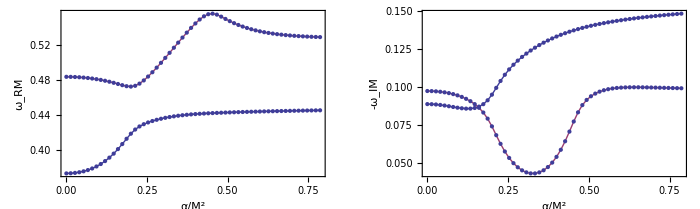

```mathematica
(***)
p1=ListPlot[{TR1,TR2},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","ω_RM"},Axes->False];
p2=ListPlot[{Abs[TI1],Abs[TI2]},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","-ω_IM"},PlotRange->All,Axes->False];
GraphicsGrid[{{p1,p2}},ImageSize->700]
```

### Higher-l

```mathematica
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)
ωguess=1.40974-0.0955096 I;(*l=7*)
ωguess=1.9916474515518394-0.287911944390142 I;(*l=10*)
ωguess=2-0.3 I;(*l=10*)
(*ωguess=0.7337751980725775-0.127070807565408 ⅈ;(*scal*)*)
(**************************************************)

f4[y_?NumericQ]:=LINCOMB[y,0,10,1 10^-3,40][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
Abs[f4[y0n]]
```

2.04925-0.10088 ⅈ

5.40477×10^-10